# Biot-Savart magnetic field calculations for wires: Tests

© 2021, Jan. G. Korvink

## Import

```mathematica
Get[NotebookDirectory[]<>"CurrentLoop2.m"]
```

## Smaller tests

#### Tests

```mathematica
MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]
```

WireSegment[{{0,0,0},{1,0,0}},1,WireColor→RGBColor[1, 0, 0]]

-Graphics3D-

Abs[ArcSinh[0.5/((0.+y)^2+(0.-z)^2)]]/5000000

√(0.+(Abs[0.-(1. (0.-y))/(((0.+y)^2+(0.-z)^2) √(0.25+(0.+y)^2+(0.-z)^2))]^2)/100000000000000+(Abs[0.+(1. (0.-z))/(((0.+y)^2+(0.-z)^2) √(0.25+(0.+y)^2+(0.-z)^2))]^2)/100000000000000)

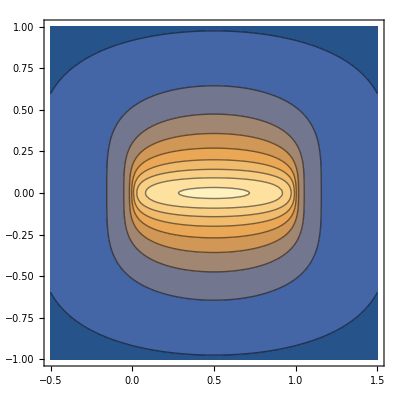

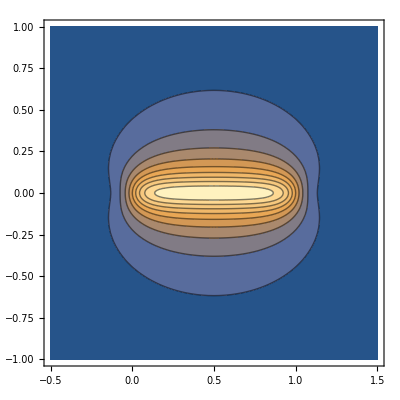

```mathematica
DrawWire[MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]]//Graphics3D
MagneticVectorPotential[{0.5,y,z}, MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]]//Norm
MagneticInduction[{0.5,y,z}, MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]]//Norm
ContourPlot[MagneticVectorPotential[{x,.1,z}, MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]]//Norm,{x,-.5,1.5},{z,-1,1},MaxRecursion->4,PlotRange->All]
ContourPlot[MagneticInduction[{x,.1,z}, MakeWireSegment[{{0,0,0},{1,0,0}},1,LoopColor->Blue]]//Norm,{x,-.5,1.5},{z,-1,1},MaxRecursion->4,PlotRange->All]
```

-Graphics3D-

RotationMatrix::spln: Vectors {0,0,-2} and {0,0,1} do not define a plane.

{(-(y ((1-z)/(√((-1+x)^2+y^2+(1-z)^2))+(1+z)/(√((-1+x)^2+y^2+(1+z)^2))))/((-1+x)^2+y^2)+(y ((1-z)/(√((1+x)^2+y^2+(1-z)^2))+(1+z)/(√((1+x)^2+y^2+(1+z)^2))))/((1+x)^2+y^2))/10000000,1/10000000((((1-x)/(√((1-x)^2+y^2+(-1-z)^2))+(1+x)/(√((1+x)^2+y^2+(-1-z)^2))) (-1-z))/(y^2+(-1-z)^2)+(((1-x)/(√((1-x)^2+y^2+(-1+z)^2))+(1+x)/(√((1+x)^2+y^2+(-1+z)^2))) (-1+z))/(y^2+(-1+z)^2)-((-1+x) ((1-z)/(√((-1+x)^2+y^2+(1-z)^2))+(1+z)/(√((-1+x)^2+y^2+(1+z)^2))))/((-1+x)^2+y^2)+((1+x) ((1-z)/(√((1+x)^2+y^2+(1-z)^2))+(1+z)/(√((1+x)^2+y^2+(1+z)^2))))/((1+x)^2+y^2)),((y ((1-x)/(√((1-x)^2+y^2+(-1-z)^2))+(1+x)/(√((1+x)^2+y^2+(-1-z)^2))))/(y^2+(-1-z)^2)-(y ((1-x)/(√((1-x)^2+y^2+(-1+z)^2))+(1+x)/(√((1+x)^2+y^2+(-1+z)^2))))/(y^2+(-1+z)^2))/10000000}

RotationMatrix::spln: Vectors {0,0,-2} and {0,0,1} do not define a plane.

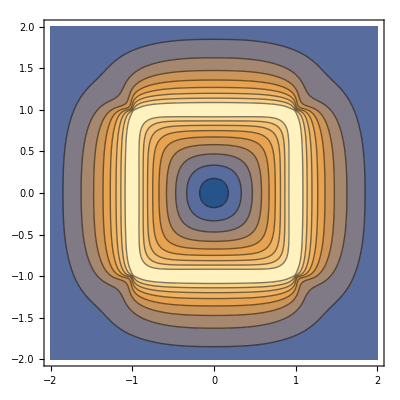

RotationMatrix::spln: Vectors {0,0,-2} and {0,0,1} do not define a plane.

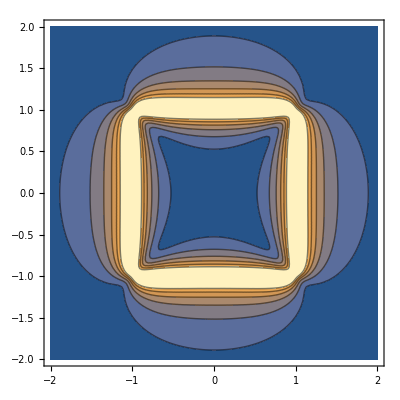

```mathematica
DrawWire[MakeWireSegment[{{-1,0,-1},{1,0,-1},{1,0,1},{-1,0,1},{-1,0,-1}},1,LoopColor->Blue]]//Graphics3D
MagneticInduction[{x,y,z}, MakeWireSegment[{{-1,0,-1},{1,0,-1},{1,0,1},{-1,0,1},{-1,0,-1}},1,LoopColor->Blue]]
ContourPlot[MagneticVectorPotential[{x,.1,z}, MakeWireSegment[{{-1,0,-1},{1,0,-1},{1,0,1},{-1,0,1},{-1,0,-1}},1,LoopColor->Blue]]//Norm,{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All]
ContourPlot[MagneticInduction[{x,.1,z}, MakeWireSegment[{{-1,0,-1},{1,0,-1},{1,0,1},{-1,0,1},{-1,0,-1}},1,LoopColor->Blue]]//Norm,{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All]
```

```mathematica
MakeWireCircle[20,1]
MakeWireCircle[20,1,LoopColor->Blue]
MakeWireCircle[{1,0,0},20,1]
MakeWireCircle[{1,0,0},20,1,LoopColor->Blue]
MakeWireCircle[{1,0,0},{1,2,3},20,1]
MakeWireCircle[{1,0,0},{1,2,3},20,1,LoopColor->Blue]
```

WireCircle[{0,0,0},{0,0,1},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircle[{0,0,0},{0,0,1},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircle[{1,0,0},{0,0,1},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircle[{1,0,0},{0,0,1},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircle[{1,0,0},{1/(√14),√(2/7),3/(√14)},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircle[{1,0,0},{1/(√14),√(2/7),3/(√14)},20,1,WireColor→RGBColor[1, 0, 0]]

```mathematica
DrawWire[MakeWireCircle[2,1]]//Graphics3D
DrawWire[MakeWireCircle[2,1,LoopColor->Blue]]//Graphics3D
DrawWire[MakeWireCircle[{1,0,0},2,1]]//Graphics3D
DrawWire[MakeWireCircle[{1,0,0},2,1,LoopColor->Blue]]//Graphics3D
DrawWire[MakeWireCircle[{1,0,0},{1,2,3},2,1]]//Graphics3D
DrawWire[MakeWireCircle[{1,0,0},{1,2,3},2,1,LoopColor->Blue]]//Graphics3D
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
MakeWireCircularArc[20,{π/4,5π/4},1]
MakeWireCircularArc[20,{π/4,5π/4},1,LoopColor->Blue]
MakeWireCircularArc[{1,0,0},20,{π/4,5π/4},1]
MakeWireCircularArc[{1,0,0},20,{π/4,5π/4},1,LoopColor->Blue]
MakeWireCircularArc[{1,0,0},{1,2,3},20,{π/4,5π/4},1]
MakeWireCircularArc[{1,0,0},{1,2,3},20,{π/4,5π/4},1,LoopColor->Blue]
```

WireCircularArc[{0,0,0},{0,0,1},{π/4,(5 π)/4},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircularArc[{0,0,0},{0,0,1},{π/4,(5 π)/4},20,1,WireColor→RGBColor[1, 0, 0]]

WireCircularArc[{1,0,0},{0,0,1},20,{π/4,(5 π)/4},1,WireColor→RGBColor[1, 0, 0]]

WireCircularArc[{1,0,0},{0,0,1},20,{π/4,(5 π)/4},1,WireColor→RGBColor[1, 0, 0]]

WireCircularArc[{1,0,0},{1/(√14),√(2/7),3/(√14)},20,{π/4,(5 π)/4},1,WireColor→RGBColor[1, 0, 0]]

WireCircularArc[{1,0,0},{1/(√14),√(2/7),3/(√14)},20,{π/4,(5 π)/4},1,WireColor→RGBColor[1, 0, 0]]

```mathematica
Graphics3D[DrawWire[MakeWireCircularArc[2,{0,3π/2},1]],Axes->True]
DrawWire[MakeWireCircularArc[2,{π/4,5π/4},1,LoopColor->Blue]]//Graphics3D
DrawWire[MakeWireCircularArc[{1,0,0},2,{π/4,5π/4},1]]//Graphics3D
DrawWire[MakeWireCircularArc[{1,0,0},2,{π/4,5π/4},1,LoopColor->Blue]]//Graphics3D
DrawWire[MakeWireCircularArc[{1,0,0},{1,2,3},2,{π/4,5π/4},1]]//Graphics3D
DrawWire[MakeWireCircularArc[{1,0,0},{1,2,3},2,{π/4,5π/4},1,LoopColor->Blue]]//Graphics3D
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
DrawWire[MakeWireCircle[20,1],WireColor->Blue]//Graphics3D
(DrawWire[{MakeWireCircle[{0,0,0},1,1],MakeWireCircle[{5,1,0},1,1],MakeWireCircle[{5,1,0},{1,2,3},1,1,WireColor->Blue]}])//Graphics3D
```

-Graphics3D-

-Graphics3D-

```mathematica
MakeWireRectangle[{1,0,0},{1,2,3},{1,2,π/8},1,WireColor->Blue]
DrawWire[MakeWireRectangle[{1,0,0},{1,2,3},{1,2,π/8},1,WireColor->Blue]]//Graphics3D
```

WireRectangle[{1,0,0},{1/(√14),√(2/7),3/(√14)},{1,2,π/8},1,WireColor→RGBColor[0, 0, 1]]

-Graphics3D-

```mathematica
Evaluate[MagneticInduction[{x,y,z},MakeWireRectangle[{1,0,0},{1,2,3},{1,2,π/8},1,WireColor->Blue]]/.{y->0}]
```

{((1/175 (-70+15 √14) Cos[π/8]+1/175 (35+30 √14) Sin[π/8]) ((-(3 z)/(√14)-(-1+x) (-1/(√14)-1))/(√((1)^2+((11)^2+(1)^2) 1)+1+1+1/1))/10000000+((1/350 (280+15 √14) Cos[π/8]+1/175 (-70+15 √14) Sin[π/8]) (1))/10000000+((-Cos[π/8]/(√14)-√(2/7) Sin[π/8]) (1))/10000000,1,(1/1+2+1)/(5000000 √14)+1+(31(11)/(10000000 √14)}
 |  |  |  |

#### Rest

```mathematica
?MakeWireCircle
```

WireCircle[{0.5,0,0.5},{0.995037,0.,0.0995037},1,1,WireColor→RGBColor[1, 0, 0]]

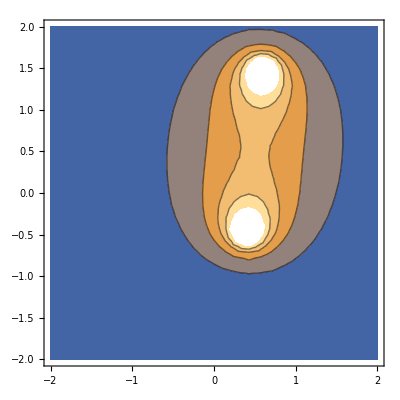

```mathematica
l=MakeWireCircle[{.5,0,.5},{1,0,.1},1,1]
f=Evaluate[MagneticInduction[{x,y,z},l]/.{y->0}]//Norm;
ContourPlot[f,{x,-2,2},{z,-2,2},AspectRatio->Automatic,Exclusions->None,MaxRecursion->2,PlotRange->{-10^-6,10^-6}]
```

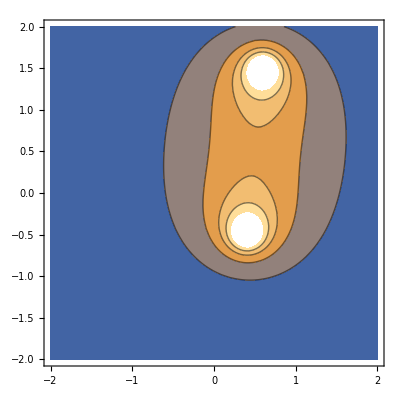

```mathematica
l=MakeWireRectangle[{.5,0,.5},{1,0,.1},{2,2,0},1];
f=Evaluate[MagneticInduction[{x,y,z},l]/.{y->0}]//Norm;
ContourPlot[f,{x,-2,2},{z,-2,2},AspectRatio->Automatic,Exclusions->None,MaxRecursion->4,PlotRange->{-10^-6,10^-6}]
```

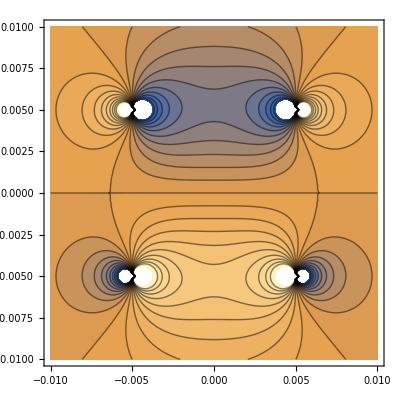

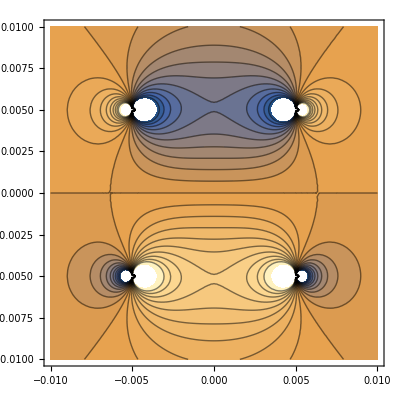

```mathematica
l={MakeWireRectangle[{0,0,-0.005},{0,0,1},{0.01,0.01,0},1],MakeWireRectangle[{0,0,0.005},{0,0,1},{0.01,0.01,0},-1]};
f=Plus@@((Evaluate[MagneticInduction[{x,y,z},#]/.{y->0}][[3]])&/@l);
ContourPlot[f,{x,-0.01,0.01},{z,-0.01,0.01},AspectRatio->Automatic,Exclusions->None,MaxRecursion->4,PlotRange->{-0.0002,0.0002},Contours->20]

l={MakeWireCircle[{0,0,-0.005},{0,0,1},0.005,1],MakeWireCircle[{0,0,0.005},{0,0,1},0.005,-1]};
f=Plus@@((Evaluate[MagneticInduction[{x,y,z},#]/.{y->0}][[3]])&/@l);
ContourPlot[f,{x,-0.01,0.01},{z,-0.01,0.01},AspectRatio->Automatic,Exclusions->None,MaxRecursion->4,PlotRange->{-0.0002,0.0002},Contours->20]
```

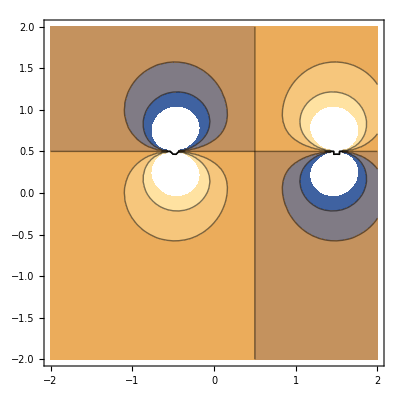
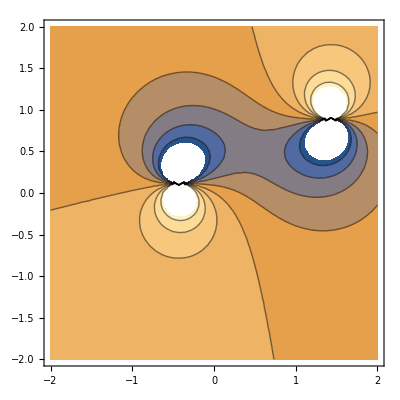
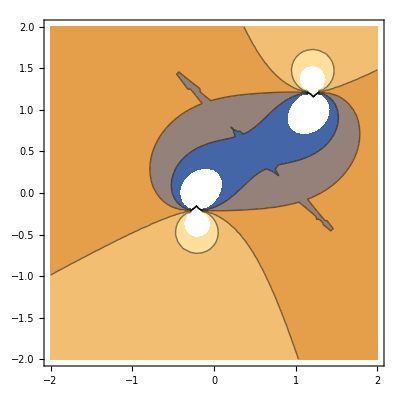
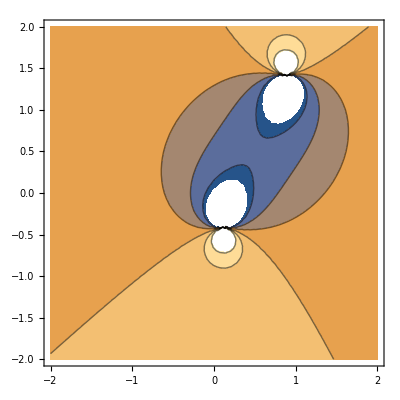
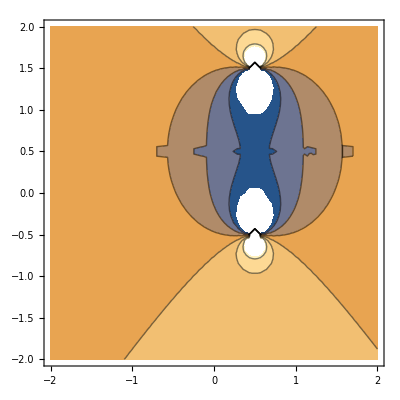
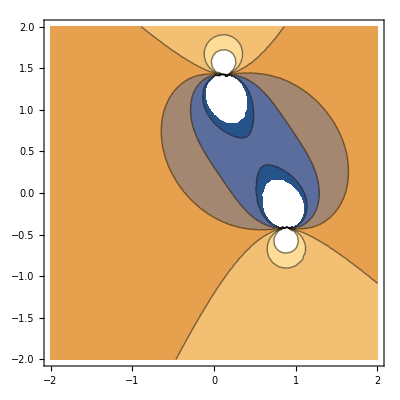
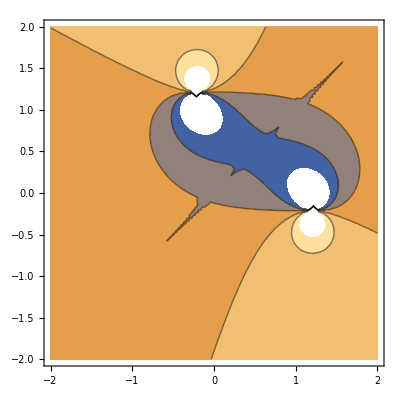
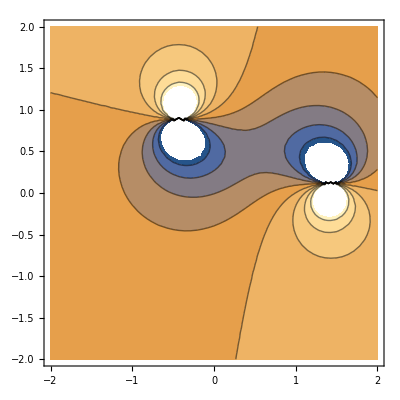

```mathematica
ContourPlot[MagneticInduction[{x,0,z},#][[1]],{x,-2,2},{z,-2,2},AspectRatio->Automatic,Exclusions->None,MaxRecursion->3]&/@(MakeWireCircle[{.5,0,.5},{Sin[#],0,Cos[#]},1,1]&/@Range[0.,7π/8.,π/8.])
```

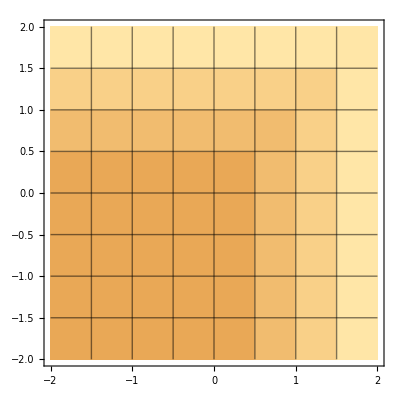
GradMagneticInduction[-Graphics-,-Graphics-]

```mathematica
l=MakeWireCircle[{.5,0,.5},{1,1,.1},1,1];
G=GradMagneticInduction[{x,y,z},l];
ContourPlot[#/.{y->0},{x,-2,2},{z,-2,2},AspectRatio->Automatic,Exclusions->None,PlotPoints->10,MaxRecursion->4]&/@Flatten[G]
```

## The conventional anti-Helmholtz gradient

```mathematica
ncoils=2; (* number of coil pairs *)
pitch=0.005; (* coil pitch and radius *)
γ=42.577 10^6; (* proton gyromagnetic ratio *)
δ=0.001; (* duration on in ms *)
currentLevel=10;

pairlist=Transpose[{currentLevel Join[Array[-1&,3],Array[1&,3]],(pitch Join[Range[-(ncoils-1)-0.1,-(ncoils-1),.05],Range[(ncoils-1),(ncoils-1)+0.1,.05]])}]
```

{{-10,-0.0055},{-10,-0.00525},{-10,-0.005},{10,0.005},{10,0.00525},{10,0.0055}}

```mathematica
coillist=MakeWireCircle[{0,0,#[[2]]},{0,0,1},pitch+0.0000,#[[1]]]&/@pairlist;
coils=Graphics3D[DrawWire[coillist],Axes->True]
{fx,fy,fz}=(Plus@@Evaluate[MagneticInduction[{x,y,z},#]&/@coillist]);
```

-Graphics3D-

```mathematica
ContourPlot[fz/.{y->0},{x,-0.01,0.01},{z,-0.01,0.01},AspectRatio->Automatic,Exclusions->None,MaxRecursion->4,PlotRange->{-0.02,0.02},Contours->20]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
θ=δ γ fz/.{y->0,x->0};
Plot[θ,{z,-0.05,0.05},Frame->True,PlotRange->All]
Plot[Mod[θ,(2π)],{z,-0.05,0.05},PlotRange->All,Frame->True]
angles=ParametricPlot3D[{pitch/2 Sin[θ],pitch/2 Cos[θ],z},{z,-6 pitch,6 pitch},PlotPoints->200,Boxed->False];
Show[{angles,coils}]

Print["Integrated angle: ",NIntegrate[θ,{z,-0.05,0.05},MaxRecursion->24]]
Print["Integrated absolute rotations: ",NIntegrate[Abs[θ]/(pitch*ncoils*2*π),{z,-(pitch*ncoils/2),(pitch*ncoils/2)},MaxRecursion->12]]
```

-Graphics-

-Graphics-

-Graphics3D-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.77556×10^-17 and 3.30155×10^-16 for the integral and error estimates.

Integrated angle: -2.77556×10^-17

Integrated absolute rotations: 12.7465

## The new gradient

```mathematica
ncoils=6; (* number of coil pairs *)
pitch=0.005; (* coil pitch and radius *)
radius=0.005; (* coil pitch and radius *)
α=42.577 10^6; (* proton gyromagnetic ratio *)
δ=0.001; (* duration on in ms *)
currentLevel=2;

pairlist=Transpose[{currentLevel Table[(-1)^n,{n,0,ncoils-1}],(pitch Range[-(ncoils-1),ncoils-1,2])}];
coillist=Flatten[{
MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0000,#[[1]]],MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0005,#[[1]]],
MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0010,#[[1]]],
MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0015,#[[1]]],
MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0020,#[[1]]],
MakeWireCircle[{0,0,#[[2]]},{0,0,1},radius+0.0025,#[[1]]]
}&/@pairlist];
coils=Graphics3D[DrawWire[coillist],Axes->True]
f=Evaluate[(Plus@@(MagneticInduction[{x,y,z},#]&/@coillist))][[3]]/.{y->0};
```

-Graphics3D-

```mathematica
Timing[ContourPlot[f,{x,-0.04,0.04},{z,-0.04,0.04},MaxRecursion->4,PlotRange->{-10^-3,10^-3}]]
```

{66.5972,-Graphics-}

```mathematica
θ=δ α f/.{y->0,x->0};
Plot[θ,{z,-0.05,0.05},Frame->True]
Plot[Mod[θ,(2π)],{z,-0.05,0.05},Frame->True]
angles=ParametricPlot3D[{pitch/2 Sin[θ],pitch/2 Cos[θ],z},{z,-12 pitch,12 pitch},PlotPoints->200,Boxed->False];
Show[{angles, coils}]
Print["Integrated angle: ",NIntegrate[θ,{z,-0.05,0.05},MaxRecursion->24]]
Print["Integrated absolute rotations: ",NIntegrate[Abs[θ]/(pitch*ncoils*2*π),{z,-(pitch*ncoils/2),(pitch*ncoils/2)},MaxRecursion->12]]
```

-Graphics-

-Graphics-

-Graphics3D-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.97071×10^-17 and 1.76448×10^-16 for the integral and error estimates.

Integrated angle: -2.97071×10^-17

Integrated absolute rotations: 3.76397